```mathematica
Needs["Palicje`"];
(* definicije *)
vozlisca = {{0,0},{1,0},{3/2,Sqrt[3]/2},{1/2,Sqrt[3]/2}};
povezave = {{2,4},{1,3,4},{2,4},{1,2,3}};
podpore={{1,{Fpx[1],Fpy[1]}},{2,{0,Fpy[2]}}};
obremenitve = {{3,{0,-1}}};
```

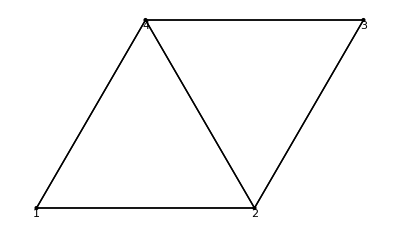

{{F[1,2]→-1/(2 √3),F[1,4]→1/(√3),F[2,3]→-2/(√3),F[2,4]→-1/(√3),F[3,4]→1/(√3),Fpx[1]→0,Fpy[1]→-1/2,Fpy[2]→3/2}}

{{F[1,2]→-1/(2 √3),F[1,4]→1/(√3),F[2,3]→-2/(√3),F[2,4]→-1/(√3),F[3,4]→1/(√3),Fpx[1]→0,Fpy[1]→-1/2,Fpy[2]→3/2}}

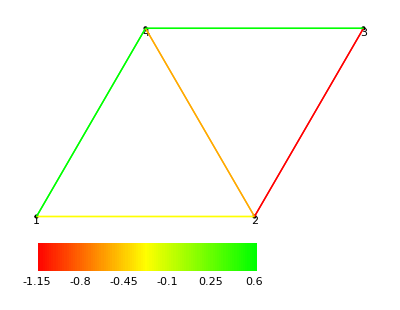

```mathematica
(* Enostavno paličje *)
NarisiPalicje[vozlisca,povezave]
enacbe = RavnovesneEnacbe[vozlisca, povezave, obremenitve, podpore];
neznanke = NeznankeSile[povezave,podpore];
Solve[enacbe,neznanke]
(* Ali tole *)
resitev=ResiPalicje[vozlisca,povezave,podpore,obremenitve]
NarisiBarvnoPalicje[vozlisca,povezave,resitev]
```

```mathematica
(* Manipulate *)
Manipulate[(
resitev=ResiPalicje[vozlisca,povezave,podpore,{{3,-F0{Sin[fi],Cos[fi]}}}];
Show[ (* options from the first graphics *)
Graphics[Arrow[{vozlisca[[3]], vozlisca[[3]]-F0/3{Sin[fi],Cos[fi]}}], PlotRange->{{-0.1,2},{-0.4,1.3}}],
NarisiBarvnoPalicje[vozlisca,povezave,resitev,-1.5, 1.5]
]),
{{F0,1}, 0, 5}, {{fi,0}, -2Pi,2Pi}]
```

```mathematica
S=GenerirajS[povezave,1];
Y=GenerirajY[povezave,1];
energija=EnergijskiFunkcional[vozlisca,povezave,obremenitve,S,Y];
vezi = Vezi[podpore];
neznanke=NeznankePomiki[vozlisca];
NMinimize[{energija,vezi},neznanke]
(* Ali tole *)
ResiPalicje[vozlisca,povezave,podpore,obremenitve,Y,S]
```

{-2.35706,{px[1]→0,py[1]→0,px[2]→-0.0330781,py[2]→0,px[3]→-0.587884,py[3]→-2.79464,px[4]→0.0371097,py[4]→-1.78639}}

{-2.35706,{px[1]→0,py[1]→0,px[2]→-0.0330781,py[2]→0,px[3]→-0.587884,py[3]→-2.79464,px[4]→0.0371097,py[4]→-1.78639}}

```mathematica
?Palicje`*
```

```mathematica
?EnergijskiFunkcional
?ResiPalicje
```

EnergijskiFunkcional[Vozlisca, Povezave, Obremenitve, Y, S] generira energijski funckional danega paličja. Y in S sta lahko bodisi konstanti bodisi Y[i, j]

ResiPalicje[Vozlisca, Povezave, Podpore, Obremenitve] določi sile v palicah za model togega paličja. 

ResiPalicje[Vozlisca, Povezave, Podpore, Obremenitve, Y, S] določi pomike vozlišč s pomočjo minimizacije energijskega funkcionala.